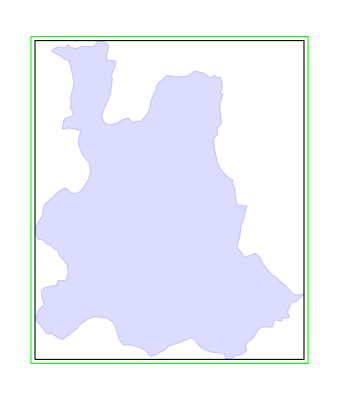

```mathematica
(*==========================*
|Load Input Data& Bounds|
*==========================*)(*Load the region boundary from a GeoTIFF file*)RegBound=QuantityMagnitude[Import["~/Dropbox/Mapping/WSF2019/WestBurkina/HouetRegion.tif",{"GeoTIFF","SpatialRange"}]][[{2,1}]];

(*Load the 100m resolution raster data and normalize*)
hou100m=Transpose[Import["~/Dropbox/Mapping/WSF2019/WestBurkina/HouetRegion100.tif","Data"]]*(1./255);

(*============================*
|Create Houet Border Polygon|
*============================*)

h=Import["~/Dropbox/Mapping/WSF2019/WestBurkina/houet.geojson"];
polygons=Cases[h,_Polygon,Infinity];
vertices=polygons/. Polygon[pts_]:>pts;
HouLatLon=Flatten[vertices,1][[2]];
HouLatLon[[All,2]]-=0.07; (*Adjust longitude*)

Hou=RegionMember[Polygon[HouLatLon]];
dim=Dimensions[hou100m];

br=BoundingRegion[Polygon[HouLatLon]];
buf=2;
bds={br[[1]]+{-buf,-buf}/110,br[[2]]+{buf,buf}/110};
reg[pt_,bds_]:=If[pt[[1]]>bds[[1,1]]&&pt[[1]]<bds[[2,1]]&&pt[[2]]>bds[[1,2]]&&pt[[2]]<bds[[2,2]],True,False];
Show[Graphics[{{EdgeForm[Blue],FaceForm[Lighter[Blue,0.1]],Opacity[0.15],Polygon[HouLatLon]},{EdgeForm[Black],FaceForm[None],br},{EdgeForm[Green],FaceForm[None],Rectangle[bds[[1]],bds[[2]]]}}]]
```

```mathematica
(*==========================*
|Define Coordinates for Raster|
*==========================*)

(*X-coordinates*)
xcoord=Table[RegBound[[1,1]]+(x-1)/(dim[[1]]-1)*(RegBound[[1,2]]-RegBound[[1,1]]),{x,dim[[1]]}];

(*Y-coordinates*)
ycoord=Table[RegBound[[2,2]]-(y-1)/(dim[[2]]-1)*(RegBound[[2,2]]-RegBound[[2,1]]),{y,dim[[2]]}];

(*==========================*
|Create 1km Resolution Raster|
*==========================*)

hou1k=Table[N[Mean[Mean[hou100m[[1+10 (i-1);;10 i,1+10 (j-1);;10 j]]]]],{i,dim[[1]]/10},{j,dim[[2]]/10}];

(*Generate corresponding coordinates for 1km raster*)
hou1kCoo=Table[{N[Mean[xcoord[[1+10 (i-1);;10 i]]]],N[Mean[ycoord[[1+10 (j-1);;10 j]]]]},{i,dim[[1]]/10},{j,dim[[2]]/10}];

(*==========================*
|Define Thresholds& Select Occupied Squares|
*==========================*)

thresholds={0.05,2/110.,5/110,0.05}; 
(*thresholds: 
1: building density in 1km squares to classify as occupied; 2: isolation distance (km from other occupied cells) to be considered as potential study village;
3: minimum distance from other study villages to be included;
4: building density in 100m squares to classify as occupied; *)

(*Select occupied 1km squares based on threshold*)
hou1kSelect=(UnitStep[hou1k-thresholds[[1]]]*hou1k)/. {0.->0};
(*Count number of occupied squares*)
Print[{"Number of occupied in region",Dimensions[hou1k][[1]]Dimensions[hou1k][[2]]-Count[Flatten[hou1kSelect],0]}];

(*Generate coordinate list of occupied cells*)
CooOccupy={};
Do[If[hou1kSelect[[i,j]]>0 &&reg[hou1kCoo[[i,j]],bds],AppendTo[CooOccupy,Flatten[{hou1kCoo[[i,j]],hou1kSelect[[i,j]],0}]]],{i,Length[hou1kSelect]},{j,Length[hou1kSelect[[1]]]}];
Print[{"Number of occupied in subregion",Length[CooOccupy]}];

(*Mark cells inside Houet region*)
Do[If[Hou[CooOccupy[[i,{1,2}]]],CooOccupy[[i,4]]=1],{i,Length[CooOccupy]}];
(*==========================*
|Select Isolated Sites|
*==========================*)
Isol={};
Do[dis=Min[Table[EuclideanDistance[CooOccupy[[i,{1,2}]],CooOccupy[[j,{1,2}]]],{j,Delete[Range[Length[CooOccupy]],i]}]];
If[dis>thresholds[[2]]&&CooOccupy[[i,4]]==1,AppendTo[Isol,i]],{i,Length[CooOccupy]}];
Print[{"number of isolated villages in Hou",Length[Isol]}];

(*==========================*
|Determine Potential Release Sites|
*==========================*)

order=RandomSample[Isol,Length[Isol]];
RelSites={CooOccupy[[order[[1]],{1,2}]]};
CooOccupy[[order[[1]],4]]=2;

Do[site=order[[i]];
dis=Min[Table[EuclideanDistance[CooOccupy[[site,{1,2}]],RelSites[[j]]],{j,Length[RelSites]}]];
If[dis>thresholds[[3]],AppendTo[RelSites,CooOccupy[[order[[i]],{1,2}]]];
CooOccupy[[order[[i]],4]]=2],{i,2,Length[order],1}];

Print[{"number of potential release sites",Length[RelSites]}];
```

{Number of occupied in region,1183}

{Number of occupied in subregion,857}

{number of isolated villages in Hou,86}

{number of potential release sites,70}

```mathematica
(*==========================*
|Assign Random Sample Data|
*==========================*)

num=Import["~/Dropbox/FieldTrials/CRT/CoordSets/No. mosq per human kpt7.csv","Table"]//Flatten;

Do[CooOccupy[[i]]=Join[CooOccupy[[i]],RandomSample[num,1]],{i,Length[CooOccupy]}];

(*Export Data*)
(*Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/Coo1K002.txt",CooOccupy,"Table"];*)
```

```mathematica
(*==========================*
|Process 100m Resolution Data|
*==========================*)
hou100mSelect=(UnitStep[hou100m-thresholds[[4]]]*hou100m)/. {0.->0};

Coo100={};
Do[If[hou100mSelect[[i,j]]>0&&reg[{xcoord[[i]],ycoord[[j]]},bds],AppendTo[Coo100,{xcoord[[i]],ycoord[[j]],hou100m[[i,j]],0,0,0}]],{i,Length[hou100mSelect]},{j,Length[hou100mSelect[[1]]]}];

Print[{"num occ hectares = ",Length[Coo100]}];
```

{num occ hectares = ,75736}

```mathematica
(*thresholds[[4]]=0.1;thresholds[[1]]=0.1;
hou100mSelect=(UnitStep[hou100m-thresholds[[4]]])/. {0.->0};
hou1kSelect=(UnitStep[hou1k-thresholds[[1]]])/. {0.->0};
Total[Flatten[hou1kSelect]]
Total[Flatten[hou100mSelect]]*)
```

658

72262

```mathematica
(*==========================*
|Assign 1km Nearest Site|
*==========================*)

posRel=Position[CooOccupy[[All,4]],2]//Flatten;
Do[pp=Nearest[CooOccupy[[All,{1,2}]],Coo100[[i,{1,2}]]][[1]];
pos=Position[CooOccupy[[All,{1,2}]],pp][[1,1]];
Coo100[[i,{4,5,6}]]={CooOccupy[[pos,5]],0,pos},{i,Length[Coo100]}];
pos=Position[CooOccupy[[All,4]],2]//Flatten;
Do[If[Hou[Coo100[[j,{1,2}]]],Coo100[[j,5]]=1],{j,Length[Coo100]}];
Do[
pt=CooOccupy[[pos[[i]],{1,2}]];
Do[If[EuclideanDistance[Coo100[[j,{1,2}]],pt]<1/110,Coo100[[j,5]]=2],{j,Length[Coo100]}];
Print[{i,pt}];
near=Nearest[Coo100[[All,{1,2}]],pt][[1]];
index=Position[Coo100[[All,{1,2}]],near][[1,1]];
Coo100[[index,5]]=3,{i,Length[pos]}];
```

{1,{-4.74954,11.2765}}

{2,{-4.70392,10.934}}

{3,{-4.66743,11.3486}}

{4,{-4.62181,11.7272}}

{5,{-4.61268,11.1864}}

{6,{-4.59443,12.0427}}

{7,{-4.59443,11.8174}}

{8,{-4.59443,11.2675}}

{9,{-4.58531,11.0963}}

{10,{-4.54881,11.7002}}

{11,{-4.54881,11.3757}}

{12,{-4.52144,10.898}}

{13,{-4.51232,11.8805}}

{14,{-4.50319,11.1233}}

{15,{-4.49407,11.3847}}

{16,{-4.47582,11.8174}}

{17,{-4.4667,11.6912}}

{18,{-4.4667,11.2315}}

{19,{-4.4302,11.2946}}

{20,{-4.4302,11.1323}}

{21,{-4.42108,10.9791}}

{22,{-4.37546,10.8889}}

{23,{-4.37546,10.7898}}

{24,{-4.35721,11.6551}}

{25,{-4.33896,10.8258}}

{26,{-4.32984,11.3126}}

{27,{-4.29334,11.601}}

{28,{-4.29334,11.0602}}

{29,{-4.28422,11.6822}}

{30,{-4.28422,11.3486}}

{31,{-4.27509,11.0061}}

{32,{-4.27509,10.7718}}

{33,{-4.26597,10.8258}}

{34,{-4.24772,11.4208}}

{35,{-4.23859,11.2946}}

{36,{-4.22947,11.8174}}

{37,{-4.22947,10.898}}

{38,{-4.2021,11.1594}}

{39,{-4.18385,11.8174}}

{40,{-4.18385,11.3486}}

{41,{-4.17473,11.7272}}

{42,{-4.17473,11.3036}}

{43,{-4.15648,11.9345}}

{44,{-4.15648,10.8168}}

{45,{-4.11998,11.2585}}

{46,{-4.09261,10.8168}}

{47,{-4.08349,11.7092}}

{48,{-4.08349,11.3036}}

{49,{-4.07436,11.7903}}

{50,{-4.07436,11.6641}}

{51,{-4.06524,10.8799}}

{52,{-4.04699,10.7898}}

{53,{-4.02874,10.9881}}

{54,{-4.00137,10.7177}}

{55,{-3.98312,11.8444}}

{56,{-3.98312,11.3847}}

{57,{-3.95575,11.0061}}

{58,{-3.95575,10.7087}}

{59,{-3.9375,11.0872}}

{60,{-3.91925,11.3036}}

{61,{-3.91925,10.7447}}

{62,{-3.91013,11.1864}}

{63,{-3.91013,10.8439}}

{64,{-3.89188,10.907}}

{65,{-3.87363,11.1503}}

{66,{-3.87363,11.0332}}

{67,{-3.85538,10.7718}}

{68,{-3.82801,10.943}}

{69,{-3.70027,10.925}}

{70,{-3.69115,10.9971}}

```mathematica
(*Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/Coo100m002.txt",Coo100,"Table"];*)
Export["~/Dropbox/FieldTrials/CRT/CRTModel/InputData/Coo100m005.txt",Coo100,"Table"];
Export["~/Dropbox/FieldTrials/CRT/CRTModel/InputData/Coo1K005.txt",CooOccupy,"Table"];
```

```mathematica
(*pos=Position[Coo100[[All,5]],2]//Flatten;
PotRel=Coo100[[pos]];
PotRel1km=Union[PotRel[[All,6]]];
Do[
pos=Position[Coo100[[All,6]],PotRel1km[[i]]]//Flatten;
Print[{i,Length[pos]}];
mean=Mean[Coo100[[pos,{1,2}]]];
near=Nearest[Coo100[[pos,{1,2}]],mean][[1]];
index=Position[Coo100[[All,{1,2}]],near][[1,1]];
Coo100[[index,5]]=3,{i,Length[PotRel1km]}];

(*Export 100m coordinate data*)
Export["~/Dropbox/FieldTrials/CRT/GeneralMetapop/InputData/Coo100m002.txt",Coo100,"Table"];*)
```

```mathematica
bds
```

{{-4.83937,10.7224},{-3.63157,12.1505}}

{29199,43119,3348,70}

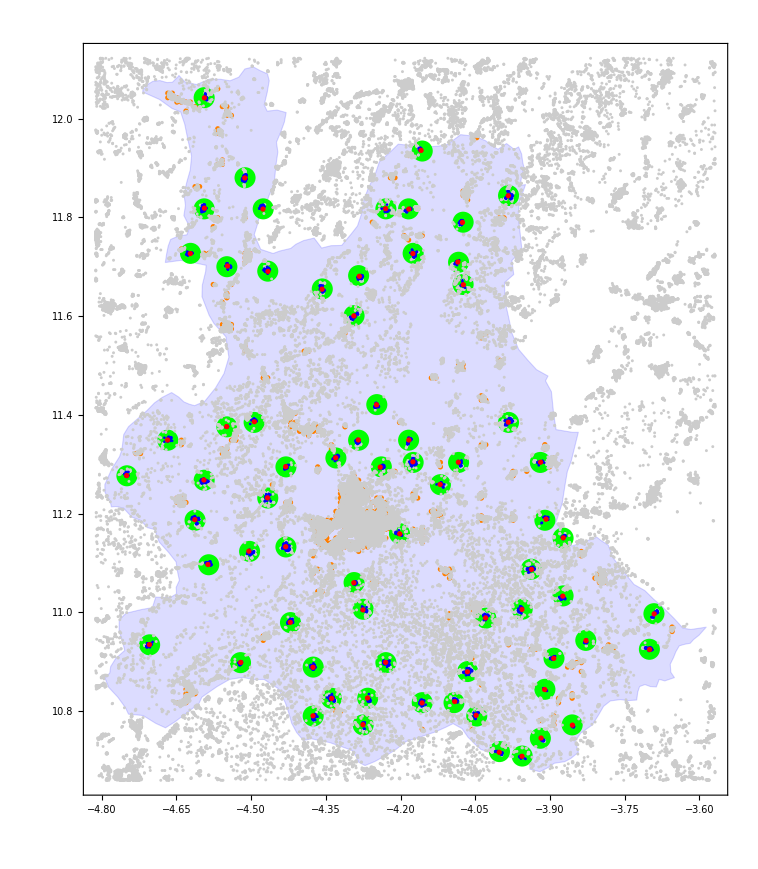

```mathematica
posall=Table[Flatten[Position[Coo100[[All,5]],i]],{i,0,3,1}];
Print[Map[Length,posall]];
posall1km=Table[Flatten[Position[CooOccupy[[All,4]],i]],{i,0,2,1}];
Show[Graphics[{EdgeForm[Blue],FaceForm[Lighter[Blue,0.1]],Opacity[0.15],Polygon[HouLatLon]}],ListPlot[Table[CooOccupy[[posall1km[[i]],{1,2}]],{i,2,Length[posall1km],1}],PlotStyle->{{Orange,PointSize[0.005]},{Green,PointSize[0.02]}}],ListPlot[Table[Coo100[[posall[[i]],{1,2}]],{i,1,Length[posall],1}],PlotStyle->{GrayLevel[0.8],GrayLevel[0.8],{Blue,PointSize[0.0025]},{Red,PointSize[0.005]}}],Frame->True,AspectRatio->dim[[2]]/dim[[1]],PlotRange->{{bds[[1,1]],bds[[2,1]]},{bds[[1,2]],bds[[2,2]]}}]
```

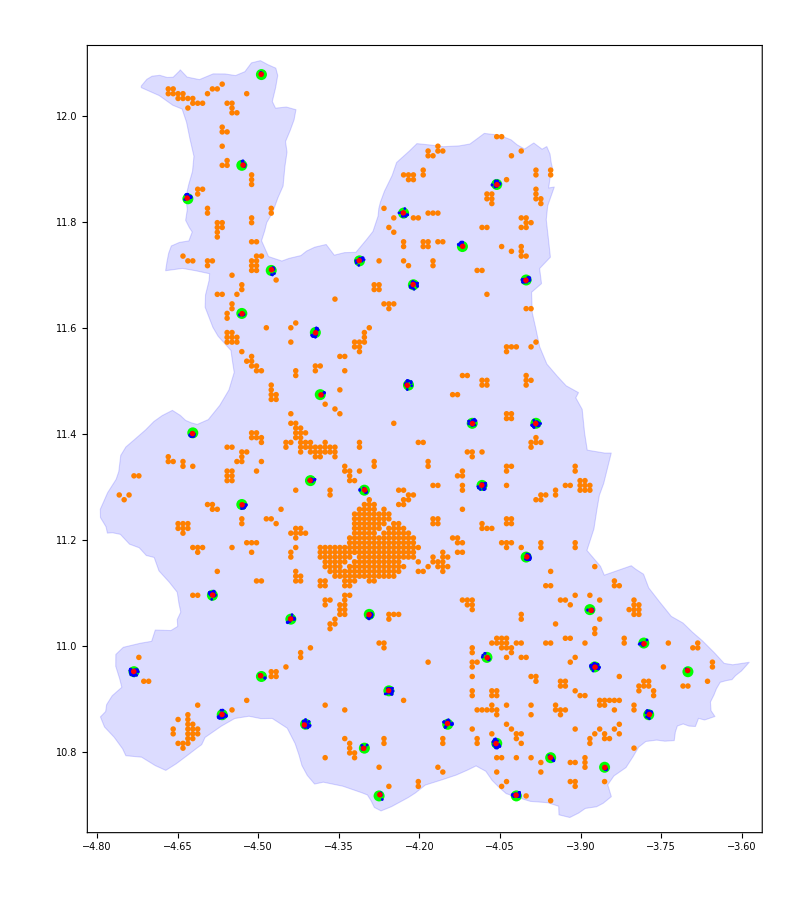

```mathematica
posall=Table[Flatten[Position[Coo100[[All,5]],i]],{i,0,3,1}];
posall1km=Table[Flatten[Position[CooOccupy[[All,4]],i]],{i,0,2,1}];
Show[Graphics[{EdgeForm[Blue],FaceForm[Lighter[Blue,0.1]],Opacity[0.15],Polygon[HouLatLon]}],ListPlot[Table[CooOccupy[[posall1km[[i]],{1,2}]],{i,2,Length[posall1km],1}],PlotStyle->{{Orange,PointSize[0.005]},{Green,PointSize[0.01]}}],ListPlot[Table[Coo100[[posall[[i]],{1,2}]],{i,3,Length[posall],1}],PlotStyle->{(*GrayLevel[0.8],GrayLevel[0.8],*){Blue,PointSize[0.0025]},{Red,PointSize[0.005]}}],Frame->True,AspectRatio->dim[[2]]/dim[[1]],PlotRange->{{First[xcoord],Last[xcoord]},{First[ycoord],Last[ycoord]}}]
```

```mathematica
dim
```

{1645,1887}

```mathematica
CooOccupy[[1;;5]]
```

{{-4.99589,11.6281,0.0470799,0,9.91388},{-4.99589,11.6191,0.011669,0,19.9712},{-4.99589,11.0422,0.0488912,0,11.3476},{-4.99589,11.0332,0.0106336,0,12.416},{-4.99589,10.9791,0.0226659,0,30.4598}}